```mathematica
q[{c11_, c13_, c33_, c44_, ρ_},p_]:=√( 1/(2 c33 c44)(c13^2 p^2-c11 c33 p^2+2 c13 c44 p^2+(c33+c44) ρ-c33 ρ √(1/(c33^2 ρ^2)((c13^2-c11 c33) (-c11 c33+(c13+2 c44)^2) p^4+2 (2 c33 c44^2+c11 c33 (-c33+c44)+c13^2 (c33+c44)+2 c13 c44 (c33+c44)) p^2 ρ+(c33-c44)^2 ρ^2))));
dq[{c11_, c13_, c33_, c44_, ρ_},p_]:=(2 c13^2 p-2 c11 c33 p+4 c13 c44 p-(4 (c13^2-c11 c33) (-c11 c33+(c13+2 c44)^2) p^3+4 (2 c33 c44^2+c11 c33 (-c33+c44)+c13^2 (c33+c44)+2 c13 c44 (c33+c44)) p ρ)/(2 c33 ρ √(1/(c33^2 ρ^2)((c13^2-c11 c33) (-c11 c33+(c13+2 c44)^2) p^4+2 (2 c33 c44^2+c11 c33 (-c33+c44)+c13^2 (c33+c44)+2 c13 c44 (c33+c44)) p^2 ρ+(c33-c44)^2 ρ^2))))/(2 √2 c33 c44 √(1/(c33 c44)(c13^2 p^2-c11 c33 p^2+2 c13 c44 p^2+(c33+c44) ρ-c33 ρ √(1/(c33^2 ρ^2)((c13^2-c11 c33) (-c11 c33+(c13+2 c44)^2) p^4+2 (2 c33 c44^2+c11 c33 (-c33+c44)+c13^2 (c33+c44)+2 c13 c44 (c33+c44)) p^2 ρ+(c33-c44)^2 ρ^2)))));
```

```mathematica
integrateNowTest[f_,offset_,{zs_,zr_},maxfreq_,model_,dList_,ω0_]:=Module[{ωc=2Pi f},
NIntegrate[
integrandk[offset,k,ωc,cijLS[#,ω0,ωc]&/@model,dList,zs,zr],{k,0,Infinity},MaxRecursion->50]

]
```

```mathematica
integrateNowFourierTest[f_,offset_,{zs_,zr_},maxfreq_,model_,dList_,ω0_]:=Module[{ωc=2Pi f},
NIntegrate[
integrandkFourier[offset,k,ωc,cijLS[#,ω0,ωc]&/@model,dList,zs,zr],{k,-Infinity,Infinity},MaxRecursion->50]

];
```

```mathematica
deltafreq=.5;
maxfreq=400;
freqvec=Table[f,{f,deltafreq,maxfreq,deltafreq}];
fricker=90;
```

```mathematica
model1=model;
model2=ReplacePart[model,{i_,6|7}->10000];
```

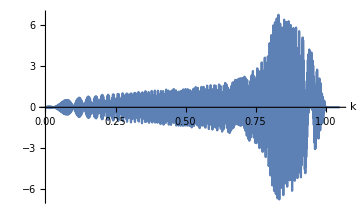
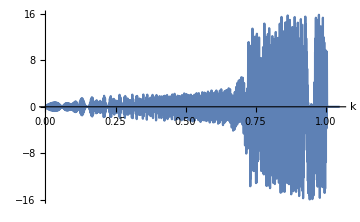

```mathematica
With[{x=2,zs=0.4,zr=0.3,ω=2Pi 400+0I},
{
Plot[
Re@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model1,dList,zs,zr],{k,0,1.05},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Re@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model2,dList,zs,zr],{k,0,1.05},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

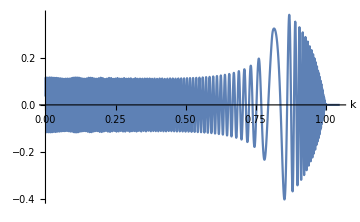
{-Graphics-,-Graphics-}

```mathematica
With[{x=1,zs=0.4,zr=0.3,ω=2Pi 400+0I,ω0=2Pi 150},
{
Plot[
Re@integrandkFourier[x,k ,ω,cijLS[#,ω0,ω]&/@model1,dList,zs,zr],{k,0,1.05},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Re@integrandkFourier[x,k ,ω,cijLS[#,ω0,ω]&/@model2,dList,zs,zr],{k,0,1.05},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

```mathematica
With[{x=1,zs=.4,zr=.3,fmax=maxfreq,fⅈ=0 10^-6 I},
integrateNowFourierTest[40+fⅈ,x,{zs,zr},fmax,model,dList,ω0]
]//RepeatedTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1.07,-0.00385903+0.00553711 ⅈ}

```mathematica
With[{x=0,zs=.4,zr=.3,fmax=maxfreq,fⅈ=10^-5 I},
singleTrace1=ParallelTable[integrateNowTest[freqvec[[i]]+fⅈ,x,{zs,zr},fmax,model1,dList,ω0],{i,1,Length@freqvec}];
(*singleTrace2=ParallelTable[Quiet@integrateNowTest[freqvec[[i]],x,{zs,zr},fmax,model2,dList,ω0,{.05,1.1}],{i,1,Length@freqvec}];*)
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
(*Export[NotebookDirectory[]<>"trace0.mc",Compress[{singleTrace1,singleTrace2}],"String"];*)
{singleTrace1,singleTrace2}=Uncompress@Import[NotebookDirectory[]<>"trace0.mc","String"];
```

```mathematica
srcF=rickerF[#,fricker]&/@freqvec;
srcF=PadLeft[srcF,1+Length@srcF];
traceF1=PadLeft[singleTrace1,Length@srcF];
traceF2=PadLeft[singleTrace2,Length@srcF];
```

```mathematica
t=(Range[Length[srcF]]-1)/(deltafreq Length[srcF])//N;
```

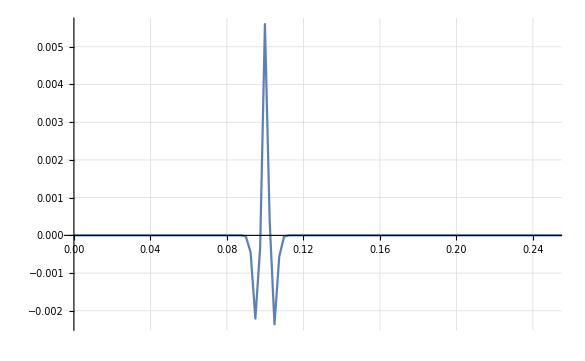

```mathematica
ListLinePlot[{t,Re@InverseFourier@(srcF (Exp[ⅈ 2Pi# .1]&/@(PadLeft[freqvec,Length@srcF])))}ᵀ,PlotRange->{{0,.25},Full},GridLines->Automatic]
```

InverseFourier::fftl: Argument {0,6.15849×10^-8 integrateNowTest[0.5,0,{0.4,0.3},400,{{11.25,6.066,11.25,2.592,1.8,500,500},{22.56,12.38,17.35,3.15,2.38,100,50},{26.73,12.51,26.73,7.11,2.22,150,100}},{0,0.358106,0},300 π,{0.05,1.1}],«48»,«751»} is not a non-empty list or rectangular array of numeric quantities.

Transpose::nmtx: The first two levels of {{0.,0.00249688,0.00499376,0.00749064,0.00998752,0.0124844,0.0149813,«37»,0.109863,0.11236,0.114856,0.117353,0.11985,0.122347,«751»},Im[InverseFourier[{«1»}]]} cannot be transposed.

InverseFourier::fftl: Argument {0,6.15849×10^-8 integrateNowTest[0.5,0,{0.4,0.3},400,{{11.25,6.066,11.25,2.592,1.8,500,500},{22.56,12.38,17.35,3.15,2.38,100,50},{26.73,12.51,26.73,7.11,2.22,150,100}},{0,0.358106,0},300 π,{0.05,1.1}],«48»,«751»} is not a non-empty list or rectangular array of numeric quantities.

Transpose::nmtx: The first two levels of {{0.,0.00249688,0.00499376,0.00749064,0.00998752,0.0124844,0.0149813,«37»,0.109863,0.11236,0.114856,0.117353,0.11985,0.122347,«751»},Im[InverseFourier[{«1»}]]} cannot be transposed.

InverseFourier::fftl: Argument {0,«49»,«751»} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of InverseFourier::fftl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.,0.00249688,0.00499376,0.00749064,0.00998752,0.0124844,0.0149813,«37»,0.109863,0.11236,0.114856,0.117353,0.11985,0.122347,«751»},Im[InverseFourier[{«1»}]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

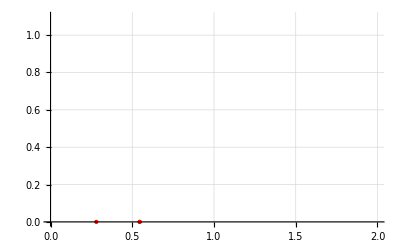

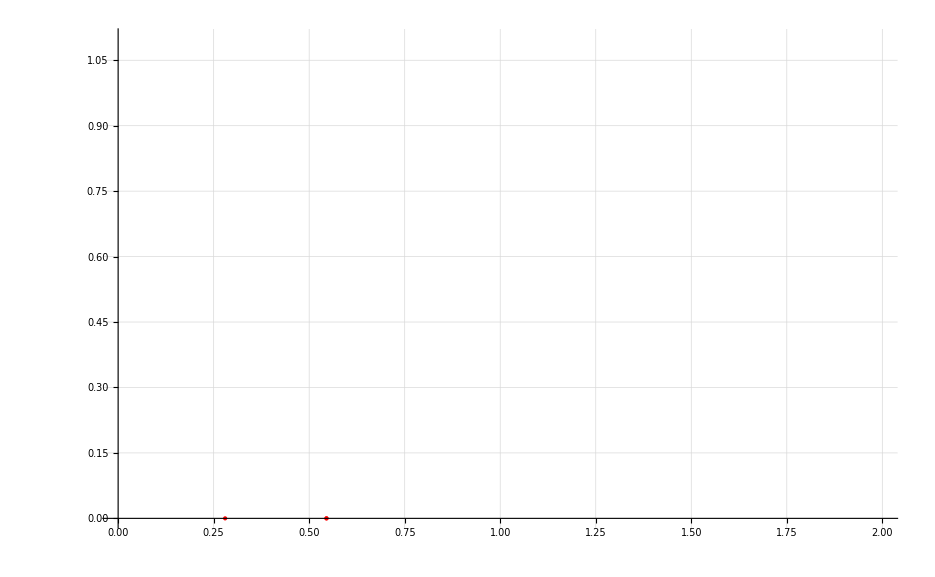

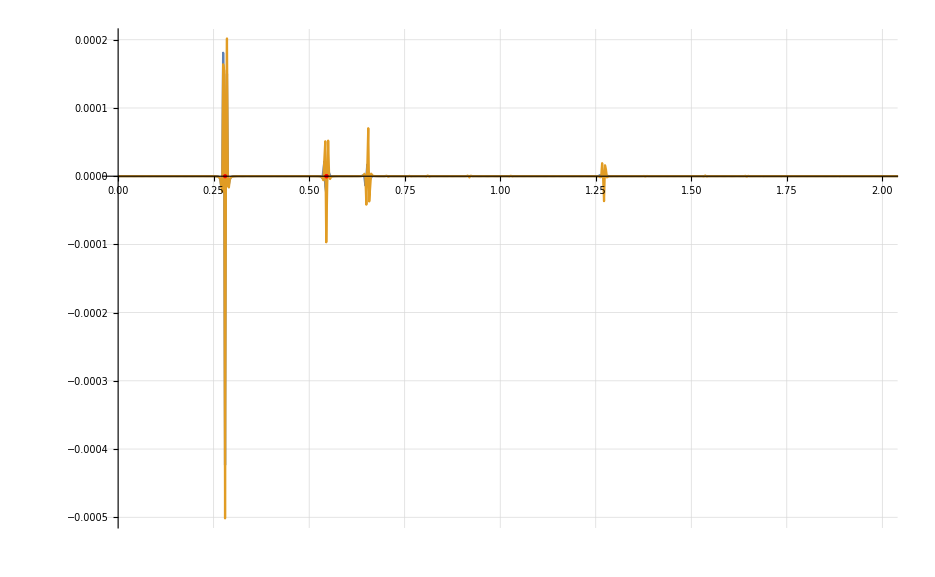

```mathematica
ListLinePlot[{{t,Im@InverseFourier@(traceF1 srcF)}ᵀ,{t,Im@InverseFourier@(traceF2 srcF)}ᵀ},PlotRange->{{0,2},Full},GridLines->Automatic,Epilog->{PointSize[Medium],Red,Point[{With[{x=0,zs=.4,zr=.3},
Join[{zs+zr},2dList[[2;;-1]]]/√(model[[;;,3]]/model[[;;,5]])//Accumulate],ConstantArray[0,Length@dList]}ᵀ
]
}]
```

```mathematica
With[{x=2,zs=.4,zr=.3,fmax=maxfreq},
singleTrace1x2=ParallelTable[Quiet@integrateNowTest[freqvec[[i]],x,{zs,zr},fmax,model1,dList,ω0,{.05,1.1}],{i,1,Length@freqvec}];
singleTrace2x2=ParallelTable[Quiet@integrateNowTest[freqvec[[i]],x,{zs,zr},fmax,model2,dList,ω0,{.05,1.1}],{i,1,Length@freqvec}];
];
```

```mathematica
(*Export[NotebookDirectory[]<>"trace2.mc",Compress[{singleTrace1x2,singleTrace2x2}],"String"];*)
{singleTrace1x2,singleTrace2x2}=Uncompress@Import[NotebookDirectory[]<>"trace2.mc","String"];
```

```mathematica
traceF1x2=PadLeft[singleTrace1x2,Length@srcF];
traceF2x2=PadLeft[singleTrace2x2,Length@srcF];
```

```mathematica
With[{zs=.4,zr=.3,x=2},
With[{mdl=Join[{Join[{zs+zr},2dList[[2;;-2]]]},model[[1;;-2]]ᵀ]ᵀ},
With[{pvec=NMinimize[#,p][[2,1,2]]&/@
Abs[x+Accumulate[#[[1]] dq[#[[2;;6]],p]&/@mdl]]},

Table[
Total[#[[1]]q[#[[2;;6]],pvec[[i]]]-pvec[[i]]#[[1]] dq[#[[2;;6]],pvec[[i]]]&/@(mdl[[1;;i]])],
{i,1,Length@mdl}]


]
]
]
```

{0.847585,0.900089}

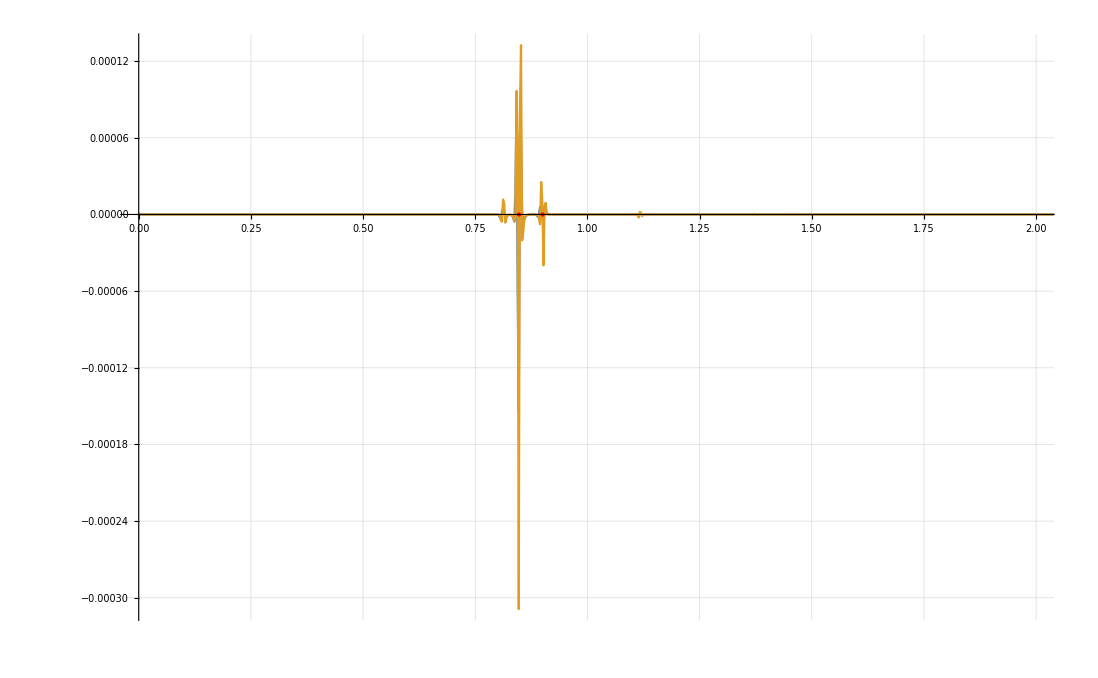

```mathematica
ListLinePlot[{{t,Re@InverseFourier@(traceF1x2 srcF)}ᵀ,{t,Re@InverseFourier@(traceF2x2 srcF)}ᵀ},PlotRange->{{0,2},Full},GridLines->Automatic,Epilog->{PointSize[Medium],Red,Point[{
With[{zs=.4,zr=.3,x=2},
With[{mdl=Join[{Join[{zs+zr},2dList[[2;;-2]]]},model[[1;;-2]]ᵀ]ᵀ},
With[{pvec=NMinimize[#,p][[2,1,2]]&/@
Abs[x+Accumulate[#[[1]] dq[#[[2;;6]],p]&/@mdl]]},
Table[
Total[#[[1]]q[#[[2;;6]],pvec[[i]]]-pvec[[i]]#[[1]] dq[#[[2;;6]],pvec[[i]]]&/@(mdl[[1;;i]])],
{i,1,Length@mdl}]
]
]
],ConstantArray[0,Length@dList-1]}ᵀ
]
}]
```